```mathematica
hbar=1.05457148×10(10)^-34; Delta = 9.2 10^12;Gam = 32.8 10^6/(2 Pi);λ = 852.1 10^-9; Inti = 2000000;Ints = 3;
alal = 2;k= 2 Pi/λ;
mCs = (133 1.660 10^-27);
Clear[a,b,x,y,z,h]
Er = hbar^2 k^2/(2*mCs)
```

1.36943×10^-28

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints)
```

-1.73542×10^-28

```mathematica
Clear[a,b,x,y,z, hbar, Gam, Inti, Ints, Delta,k]
```

```mathematica
UD[x_,y_,z_,a_,b_]:=-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}
```

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

-8.521×10^-7

At one a,b

#### Example for good grid

{0,{x→-8.521×10^-7,y→-8.521×10^-7,zf→8.521×10^-7}}

{-1.,-1.}

8.521×10^-7

-Graphics3D-

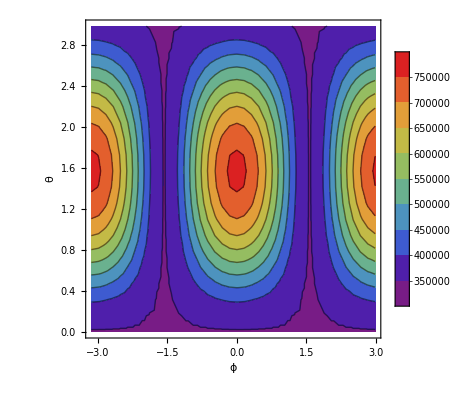

```mathematica
z=0;a= Pi/4; b = Pi/4;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10},{zf,-1 * 1λ,1* 1λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} 
{x/. mi[[2]],y/. mi[[2]]}/λ
z = zf /. mi[[2]]
goodlat = Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
goodfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

```mathematica
Second Example for good grid but secon choice
```

{0,{x→-7.6689×10^-7,y→8.521×10^-7,zf→5.9647×10^-7}}

{-0.9,1.}

5.9647×10^-7

-Graphics3D-

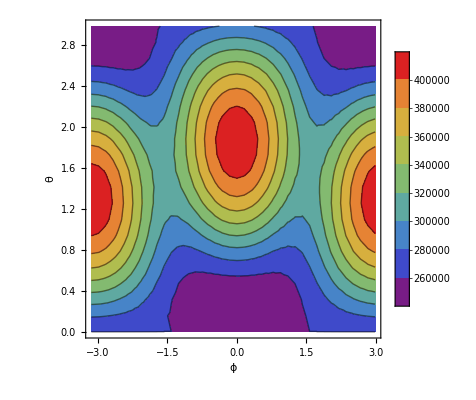

```mathematica
z=0;a= -Pi/4; b = Pi/4;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10},{zf,-1 * 1λ,1* 1λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} 
{x/. mi[[2]],y/. mi[[2]]}/λ
z = zf /. mi[[2]]
goodlat = Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
goodfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

### Example for bad grid

{-8.521×10^-7,-8.521×10^-7,-8.521×10^-7}

{0,{x→-8.521×10^-7,y→-8.521×10^-7,zf→-8.521×10^-7}}

{-1.,-1.}

-8.521×10^-7

-Graphics3D-

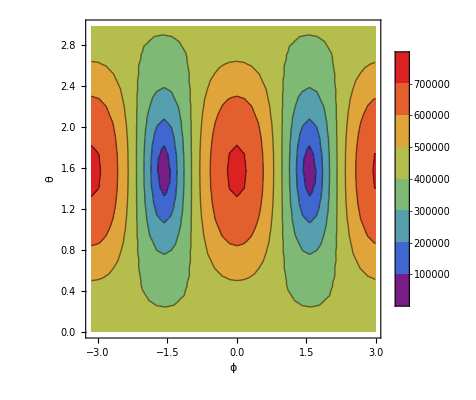

```mathematica
z=0;a= Pi/2; b = Pi/2;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10},{zf,-1 * 1λ,1* 1λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]]
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} 
{x/. mi[[2]],y/. mi[[2]]}/λ
z = zf /. mi[[2]]
badlat = Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
badfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

347683.

763985.

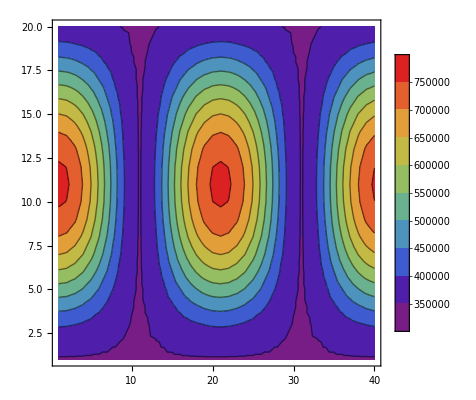

```mathematica
Show[%886,Boxed->False]
```

### Example for flirr optimum

{0,{x→-8.521×10^-7,y→-8.521×10^-7,zf→-8.521×10^-7}}

{-1.,-1.}

-8.521×10^-7

-Graphics3D-

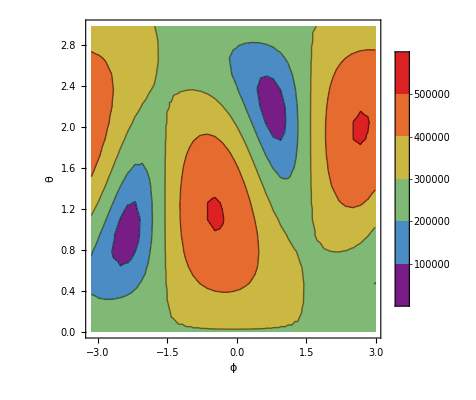

```mathematica
z=0;a= 0; b = Pi/2;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10},{zf,-1 * 1λ,1* 1λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} 
{x/. mi[[2]],y/. mi[[2]]}/λ
z = zf /. mi[[2]]
badlat = Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 1λ,1* 1λ, λ/10},{y,-1 * 1λ,1* 1λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
abola =Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

{ϕ,θ,Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]}

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
badfreq = ListContourPlot[Flatten[abola,1], PlotLegends->True, ColorFunction-> "Rainbow", FrameLabel-> {"ϕ", "θ"}]
```

## Many a,b

```mathematica
Monitor[abmat = Table[z=0;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 0.5λ,0.5* λ, λ/10},{y,-1 * 0.5λ,1* 0.5λ,λ/10},{zf,-1 * 0.5λ,1* 0.5λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} ;
(*Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 2.9λ,1* 2.9λ, λ/10},{y,-1 * 2.9λ,1* 2.9λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]*)

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
angulardata = Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
minfreq = Min[angulardata];
maxfreq = Max[angulardata];  {a,b,minfreq/maxfreq},{a,-Pi/2,Pi/2,Pi/25},{b,-Pi/2,Pi/2,Pi/25}];,{a,b}]
```

Min::nord: Invalid comparison with 0.+97694.4 ⅈ attempted.

Min::nord: Invalid comparison with 0.+97677.3 ⅈ attempted.

Min::nord: Invalid comparison with 0.+94257.4 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with 0.+31591.2 ⅈ attempted.

Max::nord: Invalid comparison with 0.+31601.1 ⅈ attempted.

Max::nord: Invalid comparison with 0.+33996.8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
abmat
```

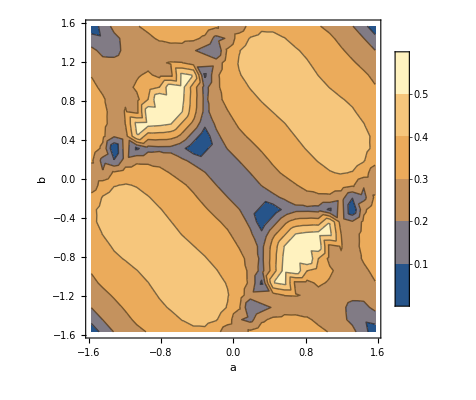

```mathematica
diffplot = ListContourPlot[Flatten[abmat,1], FrameLabel  -> {"a","b"}, PlotLegends->True]
```

```mathematica
Monitor[abmatmax = Table[z=0;
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1* 0.5λ,0.5* λ, λ/10},{y,-1 * 0.5λ,1* 0.5λ,λ/10},{zf,-1 * 0.5λ,1* 0.5λ,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}} ;
(*Show[{ListPlot3D[Flatten[Table[{x,y,UD[x,y,zf /. mi[[2]],a,b]/Er},{x,-1* 2.9λ,1* 2.9λ, λ/10},{y,-1 * 2.9λ,1* 2.9λ,λ/10}],1]],
ListPointPlot3D[{{x /. mi[[2]],y /. mi[[2]],UDsim[x/. mi[[2]],y/. mi[[2]], zf /. mi[[2]],a,b]/Er *1}}, PlotStyle->Directive[Red,PointSize[0.04]] ],
ListPointPlot3D[{{0,0,0}}, PlotStyle->Directive[Red,PointSize[0.01]] ]

}]*)

ho = 10^-10;
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
angulardata = Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

Sqrt[1/mCs 1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])]

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}];
minfreq = Min[angulardata];
maxfreq = Max[angulardata]; {a,b,maxfreq},{a,-Pi/2,Pi/2,Pi/25},{b,-Pi/2,Pi/2,Pi/25}];,{a,b}]
```

Min::nord: Invalid comparison with 0.+97694.4 ⅈ attempted.

Min::nord: Invalid comparison with 0.+97677.3 ⅈ attempted.

Min::nord: Invalid comparison with 0.+94257.4 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with 0.+31591.2 ⅈ attempted.

Max::nord: Invalid comparison with 0.+31601.1 ⅈ attempted.

Max::nord: Invalid comparison with 0.+33996.8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

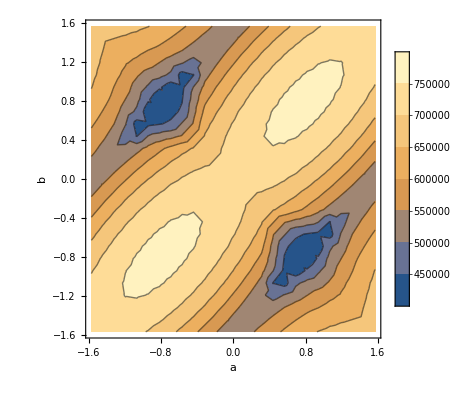

```mathematica
maxplot = ListContourPlot[Flatten[abmatmax,1], FrameLabel  -> {"a","b"}, PlotLegends -> True]
```

```mathematica
GraphicsGrid[{{maxplot, diffplot},{goodlat, badlat},{goodfreq, badfreq}}]
```

-Graphics-

Stuff

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]} //FullSimplify
```

-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-0.00008521+Abs[x]≤0,-0.00008521+Abs[y]≤0,-0.00008521+Abs[zf]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

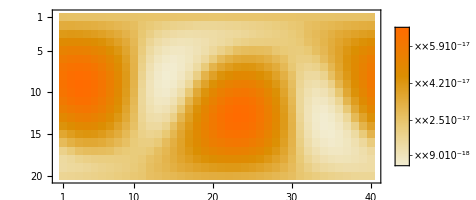

```mathematica
ho = 10^-10;  a= Pi/2; b = 0.2;
mi=Minimize[UDsim[x,y,zf,a,b],Abs[x] < 100λ &&Abs[y] < 100 λ&&Abs[zf] <100 λ,{x,y,zf}];
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
MatrixPlot[Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}], PlotLegends -> True]
```

```mathematica
mi
```

{-1.35592×10^-30,{x→-1.01178×10^-8,y→-3.26368×10^-6,zf→0.0000170615}}

```mathematica
cart = FromSphericalCoordinates[{1,1,1}]//N
```

{0.454649,0.708073,0.540302}

```mathematica
x0+ ho cart[[1]]
```

(Cos[1] Sin[1])/10000000000

```mathematica
UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]
```

```mathematica
-1.8484820715395964*^-30
 2UDsim[x0,y0 ,z0,a,b]
```

-1.84848×10^-30

-3.69696×10^-30

```mathematica
UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b]
```

```mathematica
4.640678561856709*^-37 1/ho^2
```

4.64068×10^-17

```mathematica
1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -9.99995×10^15 (3.47083×10^-31 (4+2. Cos[a]+2 Cos[0.+a+Times[«2»]]+2. Cos[b]+2 Sin[0.+a]+2. Sin[b])-1.73542×10^-31 («1»)-1.73542×10^-31 (4+Cos[a-b-0.00147475 Part[«2»]]+«5»+Sin[a-0.000737377 Part[«2»]+0.000737377 Part[«2»]])).

Hold[1/ho^2(UDsim[x0+ho cart⟦1⟧,y0+ho cart⟦2⟧,z0+ho cart⟦3⟧,a,b]-2 UDsim[x0,y0,z0,a,b]+UDsim[x0-ho cart⟦1⟧,y0-ho cart⟦2⟧,z0-ho cart⟦3⟧,a,b])]

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}//FullSimplify
```

-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])

```mathematica
LUDraw = Laplacian[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),{x,y,z}] //FullSimplify
LUDrawx = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),x],x] //FullSimplify
```

1/(3 Delta Ints)Gam^2 hbar Inti k^2 (Cos[a-b-2 k x]+Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b])

1/(6 Delta Ints)Gam^2 hbar Inti k^2 (2 Cos[a-b-2 k x]+2 Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b])

```mathematica
LUDrawy = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),y],y] //FullSimplify
```

(Gam^2 hbar Inti k^2 (Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]))/(6 Delta Ints)

```mathematica
LUDrawz = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),z],z] //FullSimplify
```

(Gam^2 hbar Inti k^2 (Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b]))/(6 Delta Ints)

```mathematica
z=0
Manipulate[ListPlot3D[Table[UD[x,y,z,0.3,0.1]/Er,{x,-1 * λ,1 * λ, λ/10},{y,-1 * λ,1 * λ,λ/10}]],{z,-1 * λ,1 * λ}]
```

0

```mathematica
a=0.1; b=0.3;z=12;Plot3D[1/Er  1/(3 Delta Ints)Gam^2 hbar Inti k^2 (Cos[a-b-2 k x]+Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b]),{x,-2 * λ,2 * λ},{y,-2 * λ,2 * λ}]
```

-Graphics3D-

```mathematica
Clear[a,b,x,y,z,k]
```

```mathematica
ⅈ*Cross[{0, Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]},{0, Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}]//FullSimplify
```

{2 (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}

```mathematica
Ufm[x_,y_,z_,a_,b_]:= 1/3{2 (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}
```

```mathematica
a=-Pi/6; b= Pi/6;z=0.5; k = 1;
Plot3D[Ufm[x,y,z,a,b][[1]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
a=0; b= Pi/2;z=0.5; k = 1;
Plot3D[Sin[a]*Cos[k*x]+Sin[b]*Cos[-k*x]+Cos[k*z],{x,-10,10},{y,-10,10}]
```